```mathematica
N[Solve[1-x1-x2/(1+x2) -x3/(1+x3) - x4/(1+x4)==0&&1-x2-x1/(1+x1) - x3/(1+x3)- x4/(1+x4)==0&&1-x3-x1/(1+x1) - x2/(1+x2)- x4/(1+x4)==0&&1-x3/(1+x3)-x1/(1+x1) - x2/(1+x2) - x4== 0, {x1, x2, x3, x4}]]
```

{{x1→-0.5,x2→1.,x3→1.,x4→1.},{x1→1.,x2→1.,x3→-0.5,x4→1.},{x1→1.,x2→1.,x3→1.,x4→-0.5},{x1→1.,x2→-0.5,x3→1.,x4→1.},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5+0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5-0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-2.59808 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5+0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.5-0.866025 ⅈ,x3→-0.5+0.866025 ⅈ,x4→-0.5-0.866025 ⅈ},{x1→-0.5+0.866025 ⅈ,x2→-0.0540541+0.324324 ⅈ,x3→-0.5-0.866025 ⅈ,x4→-0.945946-0.324324 ⅈ},{x1→-3.30278,x2→-3.30278,x3→-3.30278,x4→-3.30278},{x1→0.302776,x2→0.302776,x3→0.302776,x4→0.302776}}

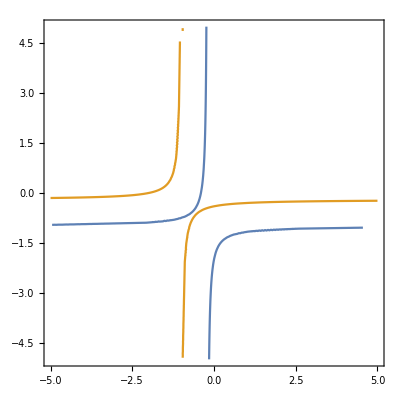

```mathematica
ContourPlot[{2+5*x1-x2/(1+x2)==0,2+5*x2-x1/(1+x1)==0 }, {x1, -5, 5}, {x2, -5, 5}]
```

```mathematica
a11 = 0.5;
N[Solve[1-a11*x1-2*(a11-1)*x2/(1+x2)==0&&1-(1-a11)*x2+2*a11*x1/(1+x1)==0 {x1, x2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→-0.561553,x2→-0.561553},{x1→3.56155,x2→3.56155}}